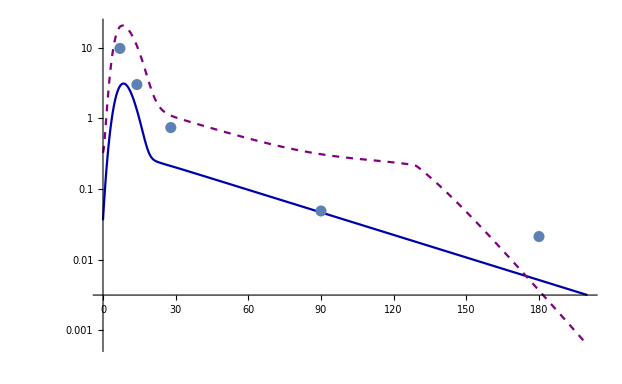

```mathematica
{μ,rE0,γE,γB,α1,α2}=(*{3.6435,5.90674,0.0460711,0.0202419,2.09147,2.18078}*){0.481,2.26078,0.003,0.03,4.29,1.35}; 
CAR0=0.36;f=0.1;
{n0,m0,e0,b0}={6.0,f CAR0,(1-f)CAR0,200.0};
carEffData={{7,14,28,90,180},{9.729,2.997,0.738,0.0486,0.02115}};
With[{rN=0.16,kN=500.0,rB=0.065,rMmax=0.414,rMmin=0.0215,kM=160,τ=18.8,T=200},
rM[t_]:=(rMmax-rMmin)/(1+Exp[-(τ-t)])+rMmin;
sol=NDSolve[{
n'[t]==-rN n[t]Log[(n[t]+m[t])/kN],
m'[t]==-rM[t] m[t]Log[(n[t]+m[t])/kM],
e'[t]==rE0(1+α1 Min[b[t]/b0,α2])m[t]-μ e[t]-γE b[t] e[t],
b'[t]==rB b[t]-γB b[t] e[t],
n[0]==n0,m[0]==m0,e[0]==e0,b[0]==b0},{n,m,e,b},{t,T}];
carMem=LogPlot[{m[t]/.sol},{t,0,200},PlotStyle->{Darker[Blue]},PlotRange->All];
carEff=LogPlot[{e[t]/.sol},{t,0,200},PlotStyle->{Purple,Dashed},PlotRange->All];
tumor=LogPlot[{b[t]/.sol},{t,0,200},PlotStyle->{Darker[Red]},PlotRange->All];
dataPlot=ListLogPlot[{carEffData[[1,#]],carEffData[[2,#]]}&/@Range[5]];
Show[carMem,carEff,dataPlot]
]
```

```mathematica
path=NotebookDirectory[]<>"../parameterEstimation/fourPopulationModelData/outputData_params_1_2019-11-14.txt";
```

```mathematica
rawdata=Import[path,"Data"];
```

```mathematica
rawdata[[1]]
```

{#(mu,rEff0,Gamma_E,Gamma_B,alpha_1,alpha_2)}

```mathematica
rawdata[[#]]&/@{21,22,23,25,26,27,28,83,84,85,86}
```

{{3.451,3.51336,0.00051818,0.00694471,5.62397,0.0391842},{3.21961,2.80398,1.95478×10^-9,0.00765953,5.08551,0.058819},{1.36845,0.797753,1.×10^-12,0.0116335,0.840258,1.10052},{1.05479,1.04521,0.0000117758,0.00860995,0.00199202,0.00735595},{0.222517,0.204961,1.00181×10^-12,0.0092673,4.21386×10^-7,3.02313×10^-7},{0.283722,0.30023,1.0004×10^-12,0.00806264,0.0000414573,7.39301×10^-10},{0.556718,0.352215,0.000135074,0.0107088,0.770898,0.781462},{1.2265,0.383072,1.×10^-12,0.161211,2.55704,0.861058},{0.239647,0.0718243,1.15089×10^-11,0.184413,2.3379,0.999447},{1.18009,0.354403,1.×10^-12,0.150448,2.56644,0.9078},{0.234834,0.0802426,1.00705×10^-12,0.139892,1.92665,0.999946}}

```mathematica
(* Good fit:
{μ,rE0,γE,γB,α1,α2}={0.559263,3.86703,0.00215856,0.0422975,2.33553,0.593097}; *)
```

```mathematica
carEffData[[1]]
```

{7,14,28,90,180}

```mathematica
m[#]+e[#]/.sol&/@{7,14,28,90,180}
```

{{22.5358},{11.9168},{1.30233},{0.355796},{0.00876837}}